# QED calculation: 1-Loop Calculation

### Initialization

```mathematica
Quit[];
```

```mathematica
$Language="English";
<<FeynArts`
<<FormCalc`

(* helicity to be averaged *)
_Hel=0;
```

FeynArts 3.10 (12 Mar 2018)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.6 (16 Apr 2018)

by Thomas Hahn

### Create Topology

> Top. 1 aebe/cede/0.m, 1 diagram

> Top. 2 aebe/cfdf/ef.m, 1 diagram

> Top. 3 aebf/cedf/ef.m, 1 diagram

> Top. 4 aebf/cfde/ef.m, 1 diagram

> Top. 5 aebf/cgdg/efegfg.m, 1 diagram

> Top. 6 aebf/cgdf/egefgf.m, 1 diagram

> Top. 7 aebf/cfdg/egefgf.m, 1 diagram

> Top. 8 aebf/cgde/fgfege.m, 1 diagram

> Top. 9 aebf/cedg/fgfege.m, 1 diagram

> Top. 10 aebe/cfdg/fgfege.m, 1 diagram

> Top. 11 aebf/cgdh/efegfhgh.m, 1 diagram

> Top. 12 aebf/cgdh/efehfggh.m, 1 diagram

> Top. 13 aebf/cgdh/egehfgfh.m, 1 diagram

> Top. 14 aebe/cfdf/efef.m, 1 diagram

> Top. 15 aebf/cedf/efef.m, 1 diagram

> Top. 16 aebf/cfde/efef.m, 1 diagram

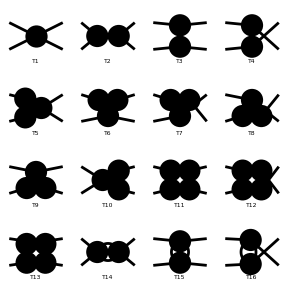

```mathematica
topo0=CreateTopologies[0,2->2];
topo1=CreateTopologies[1,2->2,ExcludeTopologies->{Internal}];
topo01=Join[topo0,topo1];
Paint[topo01, ColumnsXRows->4];
```

### e^+e^-→μ^+μ^-: QED tree-level and1-loop diagrams

loading generic model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/misho/.ghq/github.com/HEPcodes/FeynArts/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

Excluding 1 Generic, 7 Classes, and 7 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

Restoring 1 Generic, 7 Classes, and 7 Particles fields

in total: 1 Classes insertion

Excluding 1 Generic, 7 Classes, and 7 Particles fields

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 1 Classes insertion

> Top. 8: 1 Classes insertion

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 0 Classes insertions

> Top. 12: 0 Classes insertions

Restoring 1 Generic, 7 Classes, and 7 Particles fields

in total: 2 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 1 diagram

> Top. 2 aebf/cgdh/efegfhgh.m, 1 diagram

> Top. 3 aebf/cgdh/efehfggh.m, 1 diagram

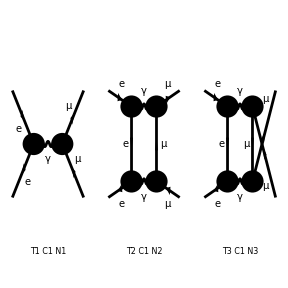

```mathematica
process={F[2,{1}],-F[2,{1}]}->{F[2,{2}],-F[2,{2}]};
TreeDiagrams = InsertFields[topo0,process,InsertionLevel->{Classes},
ExcludeParticles->{V[2],V[3],V[4],S}];
OneLoopDiagrams = InsertFields[topo1,process,InsertionLevel->{Classes},
ExcludeParticles->{V[2],V[3],V[4],S}];
FullDiagrams=Join[TreeDiagrams,OneLoopDiagrams];
Paint[FullDiagrams];
```

### Tree-level amplitude

```mathematica
ClearProcess[];
TreeMatrixSquared=Module[{amp,sq,mat},
amp = CalcFeynAmp[CreateFeynAmp[TreeDiagrams],FermionChains->VA];
sq =SquaredME[amp]//. HelicityME[amp];
mat =  sq[[1]]//.sq[[2]];
FullSimplify[4*mat /. Den[a_, b_] :> 1/(a-b),S+T+U==2ME2+2MM2]]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

> 1 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

(16 Alfa2 π^2 (3 S^2+(T-U)^2+2 S (T+U)))/S^2

Then we will calculate one-loop level amplitude, but notice that we have to execute “ClearProcess[]” before the one-loop level evaluation.
It will clear all the abbreviations / subexpressions, so we have to be sure that our tree-level result does not contain abbreviations and subexpressions.

Here, our result, which is stored as TreeMatrixSquared, has no abbreviations, so we are ready to execute ClearProcess[].

### Tree + 1-loop level amplitude

```mathematica
ClearProcess[];
FullAmp = CalcFeynAmp[CreateFeynAmp[FullDiagrams],FermionChains->VA]
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

preparing FORM code in /Users/misho/fc-amp-1.frm

running FORM...

ok

Amp[{{F[2,{1}],k[1],ME,{-Charge,LeptonNumber}},{-F[2,{1}],k[2],ME,{Charge,-LeptonNumber}}}→{{F[2,{2}],k[3],MM,{-Charge,LeptonNumber}},{-F[2,{2}],k[4],MM,{Charge,-LeptonNumber}}}][(-Alfa2 (4 C0i[cc0,S,MM2,MM2,0,0,MM2]-10 D0i[dd00,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]-4 ((ME2+MM2-U) (D0i[dd1,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd1,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd11,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd11,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])+(2 ME2+MM2-U) (D0i[dd12,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd12,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])+(ME2+2 MM2-U) D0i[dd13,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+(ME2-U) D0i[dd13,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])-6 (D0i[dd00,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+ME2 (D0i[dd22,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd22,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]))+1/2 (-(11 (ME2+MM2)-3 T) D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-Sub1 D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])-2 ((ME2+MM2-S-U) D0i[dd0,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+(ME2+MM2-U) D0i[dd0,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+Sub2 D0i[dd2,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+(2 ME2+MM2-U) D0i[dd2,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+(ME2+2 MM2-T) D0i[dd3,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+(ME2-U) D0i[dd3,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])+MM2 (-6 D0i[dd33,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-2 D0i[dd33,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]))-4 Alfa π Den[S,0]) Mat[F1]+Alfa2 ME (6 D0i[dd22,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+2 D0i[dd22,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+4 (D0i[dd12,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd12,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd2,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2])) Mat[F10]+Alfa2 ME (2 (D0i[dd2,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd2,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])+4 (D0i[dd12,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd12,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd22,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd22,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2])) Mat[F11]+Alfa2 MM (4 D0i[dd13,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]-2 (D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd3,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2])+2 (D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd3,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])-4 (D0i[dd13,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd33,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2])) Mat[F12]+Alfa2 (D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F13]-Alfa2 MM (4 (D0i[dd13,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd3,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2])-4 (D0i[dd13,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd3,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])+6 D0i[dd33,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-2 D0i[dd33,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F14]+Alfa2 (8 (D0i[dd1,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd1,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd11,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd11,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd12,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd12,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd13,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd13,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])-2 D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+6 D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F15]+Alfa2 MM (4 D0i[dd13,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]-2 (D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd3,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2])+2 (D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd3,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])-4 (D0i[dd13,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd33,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2])) Mat[F16]-Alfa2 (D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F17]+2 Alfa2 ME (D0i[dd22,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd22,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F18]+Alfa2 (2 D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-2 D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F19]-Alfa2 (D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F2]+Alfa2 (D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F20]-Alfa2 MM (2 D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-2 D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F21]-Alfa2 MM (2 D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-2 D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F22]-Alfa2 (D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F23]-Alfa2 (6 (D0i[dd00,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd00,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])+(ME2+MM2-T) (3/2 D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-3/2 D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])+2 (ME2 (D0i[dd22,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd22,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])+MM2 (D0i[dd33,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd33,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]))) Mat[F24]-2 Alfa2 MM (D0i[dd33,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd33,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F25]+Alfa2 (1/2 D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-1/2 D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F3]+Alfa2 ME MM (1/2 D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-1/2 D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F4]+Alfa2 (D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F5]+Alfa2 ME (2 (D0i[dd2,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd2,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])+4 (D0i[dd12,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd12,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd22,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd22,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2])) Mat[F6]-Alfa2 (1/2 D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-1/2 D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F7]+Alfa2 ME MM (1/2 D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]-1/2 D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]) Mat[F8]+Alfa2 ME MM (4 (D0i[dd13,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd23,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2])-4 (D0i[dd12,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd12,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd13,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd2,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd2,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd22,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd22,S,ME2,U,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd23,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd3,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2]+D0i[dd33,S,ME2,T,MM2,ME2,MM2,0,0,ME2,MM2])) Mat[F9]]

```mathematica
FullSq = SquaredME[FullAmp]//.HelicityME[FullAmp];
FullMatrixSquared =4*FullSq[[1]]//.FullSq[[2]]
```

> 625 helicity matrix elements

preparing FORM code in /Users/misho/fc-hel-1.frm

running FORM...

ok

4 (32+Alfa2 (1) (1))
 |  |  |  |

### Numerical Evaluation with LoopTools

You can load LoopTools by:

```mathematica
Install["LoopTools"]
```

====================================================
   FF 2.0, a package to evaluate one-loop integrals
 written by G. J. van Oldenborgh, NIKHEF-H, Amsterdam
 ====================================================
 for the algorithms used see preprint NIKHEF-H 89/17,
 'New Algorithms for One-loop Integrals', by G.J. van
 Oldenborgh and J.A.M. Vermaseren, published in 
 Zeitschrift fuer Physik C46(1990)425.
 ====================================================

LinkObject[…]

Now we can evaluate the Passarino-Veltman integrals with LoopTools.
For example,

```mathematica
D0i[dd1,5,1,-2,1,1,1,1,1,1,1]
```

-0.0331433-0.235571 ⅈ

So,

```mathematica
replaces=Join[
Subexpr[],
{Den[a_,b_]:>1/(a-b)},
{S->(2EE)^2,T->-(2 EE^2-ME2-MM2)+2 √(EE^2-ME2)√(EE^2-MM2)Cosθ,U->2ME2+2MM2-S-T},
{EE->125,ME->0.511*^-3,ME2->(0.511*^-3)^2,MM->0.106,MM2->0.106^2,Alfa->α,Alfa2->α^2}];
{TreeMatrixSquared,FullMatrixSquared}//.replaces/.Cosθ->0.5//FullSimplify
```

ffxc0i: infra-red divergent threepoint function, working with a cutoff    1.0000000000000000     
 ffxdbd: using IR cutoff lambda^2 =    1.0000000000000000

{197.392 α^2,α^2 (197.392+α (1376.86+2487.51 α))}

Note that the IR-divergence is detected.
You should be aware of the IR/UV divergences BEFORE you write computation code!

We can verify the presence of IR divergence by changing λ^2 (fictitious photon mass).
The result does depend on λ^2, so IR divergence is not cancelled.

```mathematica
SetLambda[1];
Chop[FullSimplify[FullMatrixSquared//.replaces/.Cosθ->0.5]]
SetLambda[0.1^2];
Chop[FullSimplify[FullMatrixSquared//.replaces/.Cosθ->0.5]]
SetLambda[10^2];
Chop[FullSimplify[FullMatrixSquared//.replaces/.Cosθ->0.5]]
```

α^2 (197.392+α (1376.86+2487.51 α))

α^2 (197.392+α (2012.63+5216.77 α))

α^2 (197.392+α (741.095+782.1 α))

In dimensional regularization, it will be

```mathematica
constant=FullMatrixSquared/.{C0i[__]->0,D0i[__]->0}//.replaces/.Cosθ->0.5;

SetLambda[-2];
pole2=FullMatrixSquared//.replaces/.Cosθ->0.5;
SetLambda[-1];
pole1=FullMatrixSquared//.replaces/.Cosθ->0.5;
SetLambda[0];
finite=FullMatrixSquared//.replaces/.Cosθ->0.5;
Collect[Chop[Expand[(pole2-constant)/ϵ^2+(pole1-constant)/ϵ+finite]],α]//Expand
```

197.392 α^2+1376.86 α^3+2487.51 α^4-(138.056 α^3)/ϵ+(24.139 α^4)/ϵ